```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (10-Nov-2012)) loaded Sat 10 Nov 2012 19:18:03
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

## SimRange-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

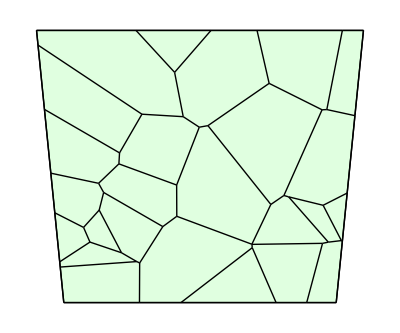

```mathematica
w=TemplateRandom[25, {{0,0}, {10,0}, {11, 10}, {-1, 10}}];
ShowTissue[w]
```

## Set up a model and run a simulation

```mathematica
n=NTissueCells[w]; 
net={{∅⇄A,k1, k2},{2 A+B->3 A,k3},{A->B,k4}, {A-> A+X, 1}};
parameters={k1-> .1, k2-> .1, k3-> .1 ,k4-> .3};
ic[i_]:={A[i]->RandomReal[{0,5}],B[i]->RandomReal[{0,5}], X[i]-> 0};
myic=Flatten[ic/@Range[n]];
bignet=CelleratorNetwork[w, "Reactions"-> net, "Diffiusion"-> {{A,DA}, {B, DB}}];
```

25 Cells.

5 internal reactions in each cell.

125 intracellular reactions.

0 diffusion reactions.

125 total reactions.

```mathematica
sim=RunSim[bignet/.{DB->.05, DA-> .1},parameters,myic,{0,50}];
```

## Use SimPlot to plot everything

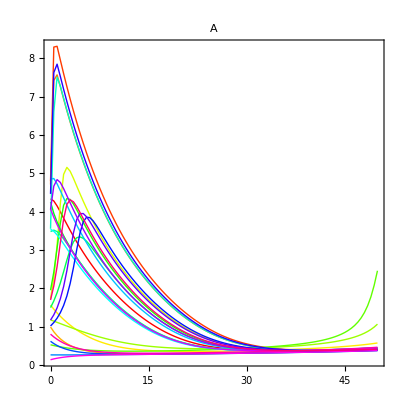
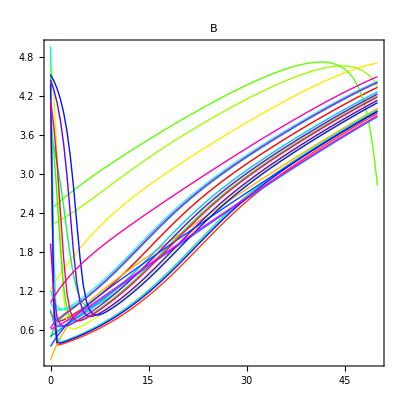
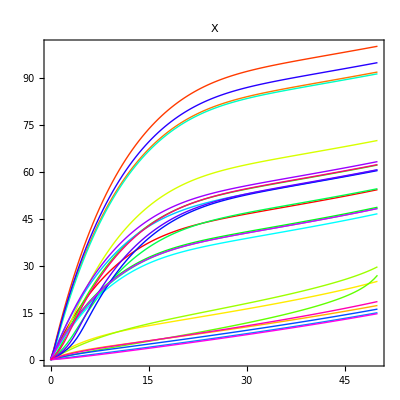

```mathematica
SimPlot[sim]
```

## Use SimRange to get range of values

```mathematica
SimRange[sim, A, 10]
```

{0.265585,3.69436}

Get the range of A over the times {0, 1, 2, 3, 4, 5,  ... ,48,  49,  50}

```mathematica
SimRange[sim, A, {0, 50, 1}]
```

{0.134967,8.31177}

Get the range of A over the times {0, 10, 20, 30, 40, 50}

```mathematica
SimRange[sim, A, {0, 50, 10}]
```

{0.134967,4.85101}